## Cosmology — Problem Set 8 — Stones and Raindrops — Solution

All four problems on this problem set emphasize that map speed |dr/dt| is very different from the speed that any observer sees. That is one of the largest points the authors are making in Chapter 6. Map speed does converge with observed speed at ∞.

Similarly, map energy is not observable. However, late in the chapter the authors argue that there is an important use of map energy. They argue that when a spherical shall having map energy E falls into a black hole, the resulting black hole ends up with mass M+E.

### Problem 1 — TWB Problem 6-2

This is a comfort problem wherein you just have to plug in values to formulas.

Use M=10km, and assume that a stone falling from rest far away from the black hole is going radially inward as it passes observers at Schwarzschild r=50km and 25km.

The assumptions mean that we get to use our formulas for raindrops.

A. What is the speed, v_shell, of the stone at r=50km?

In the text and in the Rain from Stones handout, we found that:

v_shell=(Δ y_shell)/(Δ t_shell)=-((2M)/(r̄))^(1/2)

The minus sign just means that it is moving inward.

Plugging in to get the speed we have:

((2M)/(r̄))^(1/2)=((2·10km)/(50km))^(1/2)=(0.4)^(1/2)=0.63.

B. What is |Δr/Δt| of the stone at r̄=50km?

Now we are using, r and t, which are Schwarzschild coordinates, not shell coordinates. The formula is completely different:

|Δr/Δt|=(1-(2M)/(r̄))((2M)/(r̄))^(1/2)

Plugging in, we have |Δr/Δt|=(1-(2M)/(r̄))((2M)/(r̄))^(1/2)=(1-0.4)(0.4)^(1/2)=0.38.

C. Repeat A but with r̄=25km.

((2M)/(r̄))^(1/2)=((2·10km)/(25km))^(1/2)=(0.8)^(1/2)=0.89.

D. Repeat B but with r̄=25km.

(1-0.8)(0.8)^(1/2)=0.18.

E. The particle is approaching the speed of light according to observers in shell frames, as it gets closer to the event horizon. However, according to somebody using Schwarzschild coordinates, the particle is stalling out in those coordinates! One contribution to this, is that Schwarzschild-t corresponds to observable time only very far from the black hole, and we know those people are aging faster. So of course they say things happening near the black hole are happening slower. However, the distortion of Schwarzschild-r also contributes. A small change in Schwarzschild-r just outside the event horizon, corresponds to a large change in position measured with meter sticks. These effects compound to give a dramatic difference between Δr/Δt and (Δ y_shell)/(Δ t_shell).

### Problem 2 — TWB Problem 6-4

I overlooked that this problem had a Parts D and E. I did not mean to assign those (at least not without explaining some of the physics ideas of a gas of hot electrons that the authors are utilizing!).

A. Elsewhere, we have found that the mass of the Sun, expressed as a length, is
M_Sun=1.48 10^3 m. So this hypothetical, non-rotating neutron star, which has mass 1.4 times this has M_(neutron star)=1.4 M_Sun=2.07km. Let’s just round that to 2km. That means its event horizon is at Schwarzschild-r of 4km. This is 40% of its radius (of course it depends on how you measure its radius!), but naively, 4km is 40% of 10km.

B. Someone standing on the surface would see v_shell=(Δ y_shell)/(Δ t_shell)=-((2M)/(r̄))^(1/2). The minus sign corresponds to the fact that the stone is falling inward. The speed is ((2M)/(r̄))^(1/2)=((4km)/(10km))^(1/2)=(0.4)^(1/2)=0.63, just as in the previous problem’s Part A. It matters not that the neutron star has not collapsed into a black hole. At a distance of 10km, its effects are the same as if it had.

C. |Δr/Δt|=(1-(2M)/(r̄))((2M)/(r̄))^(1/2) is the same as in the previous problem’s part B, which was 0.38.

D. KE=E-m=m(γ-1). So  KE/m=γ-1=1/((1-v_shell^2)^(1/2))-1=1/(1-2M/r̄)^(1/2)-1=1/(1-4km/10km)^(1/2)-1=1/(0.6)^(1/2)-1=0.29.

### Problem 3 — TWB Problem 6-7

On both this problem and the next problem the part of the problem where you find the maximum of |dr/dt|was not particularly instructive given the amount of algebra involved. I told some people they should skip that if pressed for time. If you correctly found the maximum, I will make that extra credit. I have put that part of my solution into an appendix titled “Extra Credit.”

First we need to put the initial conditions into Eq. 8. I write Eq. 8 as:

E/m=(1-(2M)/(r̄))Δt/Δτ

We know that Δt=(1-(2M)/(r̄))^(-1/2)Δ t_shell from Chpt. 5, Eq. 9. And we know that the particle has no velocity, and so Δ t_shell=Δτ when r̄=r_0. So putting all of three of those equations together, we find out what E/m is:

E/m=(1-(2M)/r_0)^(1/2)

Now I have used the initial conditions to discover E/m, and I am ready to launch into the questions asked.

When writing this solution, I found it easier to start with parts B and C and then to return to part A.

B. Derive an expression for the shell velocity of the stone as a function of r̄.

Looks like we just need to solve Eq. 12, which is

E_shell/m=1/((1-v_shell^2)^(1/2))=(1-(2M)/(r̄))^(-1/2)E/m=(1-(2M)/(r̄))^(-1/2)(1-(2M)/r_0)^(1/2),

for v_shell:

1-v_shell^2=(1-(2M)/(r̄))(1-(2M)/r_0)^-1

v_shell^2=1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1

For an inward-falling stone, we want the minus sign when we take the square root:

v_shell=-(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2)

As a kicker to Part B, TWB asked us to check that if we put r_0=∞ in, that we get back Eq. 19, and indeed we do:

v_shell=-((2M)/(r̄))^(1/2) (only valid for a raindrop)

C. Graph shell speed vs. r for three cases, r_0=10M, r_0=6M, r_0=3M.

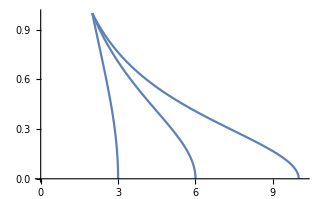

```mathematica
plot10=Plot[(1-(1-2/r)/(1-2/10))^(1/2),{r, 2, 10},PlotRange->{{0, 10.2},{0, 1}}];
plot6=Plot[(1-(1-2/r)/(1-2/6))^(1/2),{r, 2, 6},PlotRange->{{0, 10.2},{0, 1}}];
plot3=Plot[(1-(1-2/r)/(1-2/3))^(1/2),{r, 2, 3},PlotRange->{{0, 10.2},{0, 1}}];
Show[plot10,plot6,plot3]
```

Finally, I return to part A.

A. What is Δr/Δt?

Δr/Δt=Δr/(Δ y_shell)(Δ y_shell)/(Δ t_shell)(Δ t_shell)/Δt=(1-(2M)/(r̄))v_shell

where I have used Eqs. 9 and 10 from p. 5-15 to simplify two of the ratios. Now you see why I did this part last, because I have an expression for v_shell from Part B. So let’s put that in:

Δr/Δt=-(1-(2M)/(r̄))(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2)

TWB want to know where the speed is greatest. That part of my solution, I have put in an appendix.

As a kicker to Part A, TWB asked us to check that if we put r_0=∞ in, that we get back Eq. 22, and indeed:

Δr/Δt=-(1-(2M)/(r̄))(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2) is just Δr/Δt=-(1-(2M)/(r̄))((2M)/(r̄))^(1/2) (only valid for a raindrop).

### Problem 4 — TWB Problem 6-8

Just as in TWB 6-7 we need to put the initial conditions into Eq. 8:

E/m=(1-(2M)/(r̄))Δt/Δτ

This time the initial condition is at ∞ the speed is v_far. But at ∞, (1-(2M)/(r̄)) is just 1, and Δt/Δτ=γ_far where γ_far≡1/(√(1-v_far^2)). Isn’t absolutely everything the same except in the previous problem, where we had E/m=(1-(2M)/r_0)^(1/2), now I have E/m=γ_far?

So we can just write down the answers!

A. Δr/Δt=-(1-(2M)/(r̄))(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2) becomes Δr/Δt=-(1-(2M)/(r̄))(1-(1-(2M)/(r̄))(1-v_far^2))^(1/2)

B. v_shell=-(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2) becomes v_shell=-(1-(1-(2M)/(r̄))(1-v_far^2))^(1/2)

C. Graph shell speed vs. r for three cases, v_far=0.2, v_far=0.6, v_far=0.9

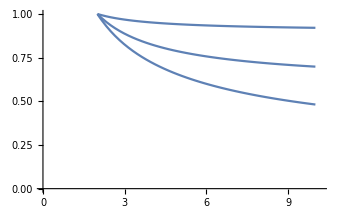

```mathematica
plotPoint2=Plot[(1-(1-2/r)(1-0.04))^(1/2),{r, 2, 10},PlotRange->{{0, 10.2},{0, 1}}];
plotPoint6=Plot[(1-(1-2/r)(1-0.36))^(1/2),{r, 2, 10},PlotRange->{{0, 10.2},{0, 1}}];
plotPoint9=Plot[(1-(1-2/r)(1-0.81))^(1/2),{r, 2, 10},PlotRange->{{0, 10.2},{0, 1}}];
Show[plotPoint2,plotPoint6,plotPoint9]
```

### Appendix — Extra Credit — Finding the maximum |dr/dt|

TWB want to know where the speed is greatest.  That we can get with calculus (or more painstakingly if you go through the small Δr approximation). The calculus way:

d/(d r̄)[(1-(2M)/(r̄))(1-(1-(2M)/(r̄))(1-(2M)/r_0)^-1)^(1/2)]=0.

But the only way that r̄ shows up is in the combination (1-(2M)/(r̄)), so let’s call that x and set d/dx[(x(1-x/x_0))^(1/2)]=0, where x_0=1-(2M)/r_0. The equation is (1-x/x_0)^(1/2)+1/2 x/(1-x/x_0)^(1/2)(-1/x_0)=0. So (1-x/x_0)-1/2 x/x_0=0 or 1=3/2 x/x_0, so x=2/3 x_0. The greatest speed is 2/3(x_0(1-2/3))^(1/2)=2/(3 √3)x_0. Putting back in r̄ and r_0, we have 1-(2M)/(r̄)=2/3(1-(2M)/r_0) or (2M)/(r̄)=1/3+2/3(2M)/r_0 or  r̄=2M/(1/3+2/3(2M)/r_0) and the greatest (most negative) Δr/Δt is -2/(3 √3)(1-(2M)/r_0).

TWB also like it if we recover the r_0=∞ limit. If we put in r_0=∞, then  r̄=2M/1/3=6M, but if we differentiate (1-y)y^(1/2) with respect to y where y=(2M)/(r̄) and set that to zero, we get -y^(1/2)+ (1 - y)1/2/y^(1/2)=0 or -y+ (1 - y)1/2=0 or 3/2 y=1/2  or  y=1/3  and putting back in y=(2M)/(r̄), we have 1/3=(2M)/(r̄)or r̄=6M.

Similarly, for the last problem, TWB want to know where Δr/Δt is greatest (more precisely, most negative). It is at:

1-(2M)/(r̄)=2/3(1-v_far^2) or r̄=(2M)/(1-2/3(1-v_far^2)).

They want to know what the greatest (most negative) Δr/Δt is. It is:

-2/(3 √3)(1-v_far^2).